```mathematica
(*** EXAMPLE FILE for QuaILS: Apochromatic plasma lens lattice ***)
(*** Author: Carl A. Lindstrom, Uni Oslo, 28.09.2016           ***)

(* IMPORT QuaILS *)
Clear["Global`*"];
Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"QuaILS_1.0.m"}]];

(* CONSTANTS *)
SIc=299792458;
SIe=1.60217662*^-19;
SIme=9.10938356*^-31;
SIϵ0=8.85418782*^-12;
SIμ0=1/(SIc^2*SIϵ0);

(* PARAMETERS *)
E0=0.205;(* [GeV] beam energy *)
r=0.001; (* [m] lens radius *)
d1=1;(* [m] lens separations *)
l=0.033;(* [m] lens length *)
β0=0.023; (* [m] initial beta function *)
k[I0_,r_,E0_]:=SIc*SIμ0*I0/(2*r^2*E0*1*^9); (* [m^-2] magnetic field strength for a plasma lens *)

(* LATTICE DEFINITION using thick, radially symmetric lenses *)
tlat=ThickLattice[{d1,d2},{k[I1,r,E0],k[I2,r,E0]},{l,l/2},False]; (* define half-lattice *)
fullLat=SymmetricLattice[tlat];(* symmetrize the half-lattice *)

(* FREE VARIABLES for matching *)
vars={I1,I2,d2}

(* BEAM DEFINITION *)
input[δ_:0]:=TwissParams[β0,β0,0,0];(* input Twiss parameters: can be energy dependent *)

(* CONSTRAINTS: α=0 and ∂α/∂δ=0 *)
fileID="example";
constraints={αx[R[tlat],input[]],Module[{δ},SeriesCoefficient[αx[Rexpand[tlat,δ,1],input[]],{δ,0,1}]]};
WriteMatlabConstraints[constraints,vars,fileID] (* write constraints to file *)

(* MERIT FUNCTION: minimize second order chromaticity, ∂^2α/∂δ^2 *)
meritFunction=Module[{δ},SeriesCoefficient[αx[Rexpand[tlat,δ,2],input[]],{δ,0,2}]]^2;
WriteMatlabMeritFunction[meritFunction,vars,fileID] (* write merit function to file *)
```

{I1,I2,d2}

/Users/calind/PhD/QuaILS/matlab/constraints/constraints_example.m

/Users/calind/PhD/QuaILS/matlab/meritfunctions/meritfunction_example.m

```mathematica
(* DEFINE MINIMIZATION PARAMETERS *)
lowers={0,-330,0}; (* lower limits *)
uppers={330,330,4}; (* upper limits *)
Ntry=10;(* max attempts without success *)
Ntotal=50;(* max attempts total *)
Niter=10000;(* number of minimization iterations *)
WriteMatlabMatchingParams[lowers,uppers,Ntry,Ntotal,Niter];

(* PERFORM NUMERICAL SOLVING in MATLAB *)
sol=RunMatlabMinimizer[vars,{},fileID];(* run MATLAB: get best solution *)
solLat=fullLat/.sol; (* solution lattice found by MATLAB *)
```

>> SHOTGUN MINIMIZATION for PERTURBATIVE CHROMATICITY CORRECTION
Searches parameter space using shotgun approach.
--- Tolerance: 1e-10 (func.), 1e-10 (params), Evals: 10000 ---
--- Max attempts: 50 (total), 10 (same step) ---
--- Upper limits: [330 330 4] ---
--- Lower limits: [0 -330 0] ---
> 1 attempts made.
Min. value: 1.99e+06 -- [40.1 -73.9 4] (match: 8.6037e-26)
> 10 unsuccessful attempts made.
 
BEST SOLUTION: 1.99e+06 : [40.13 -73.87 4]

{I1→40.1256189173800308,I2→-73.8690667592655501,d2→4.}

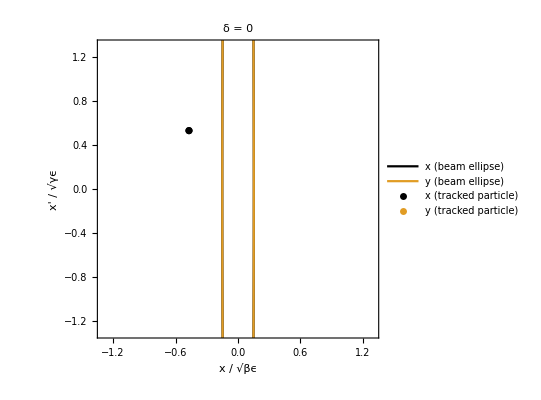

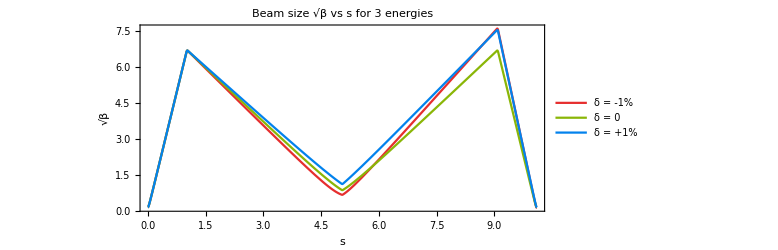

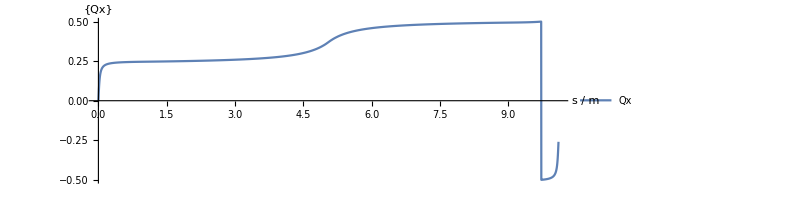

-Graphics3D-

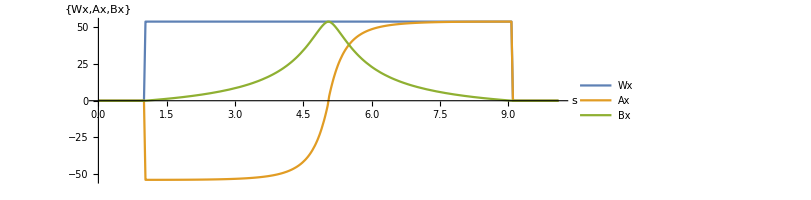

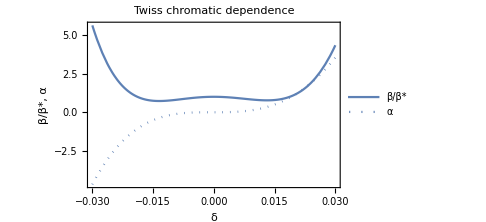

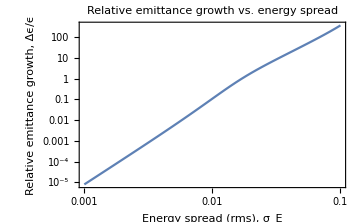

Energy spread 0.5% rms → Δϵ/ϵ = 0.00550147

Energy spread 1.% rms → Δϵ/ϵ = 0.108576

Energy spread 2.% rms → Δϵ/ϵ = 1.84406

Energy spread 4.% rms → Δϵ/ϵ = 17.7953

```mathematica
(* PLOTS *)
TriBeamSize[solLat, input, 0.01] (* plot beam size with ±1 energy offset *)
PlotLatticeFunctions[solLat,input,{Qx}] (* plot phase advance/tune*)
PlotBeamSize3D[solLat, input] (* visualize in 3D *)
PlotChromaticLatticeFunctions[solLat,input,{Wx,Ax,Bx}] (* W-function and its components *)
PlotChromaticDependence[solLat,input,input,0.03,6] (* chromatic focusing dependence *)
PlotEmittanceGrowth[solLat, input,0.001,0.1,20] (* plot relative emittance growth vs. energy spread *)
PrintEmittanceGrowths[solLat,input,{0.005,0.01,0.02,0.04}] (* print emittance growths *)
```